```mathematica
simple[a_,L_] = e^(a L) - Sum[e^(a n),{n,1,L-1}] - Sum[e^(-a n),{n,1, L}]
```

ⅇ^(a L)+(ⅇ^a-ⅇ^(a L))/(-1+ⅇ^a)-(ⅇ^(-a L) (-1+ⅇ^(a L)))/(-1+ⅇ^a)

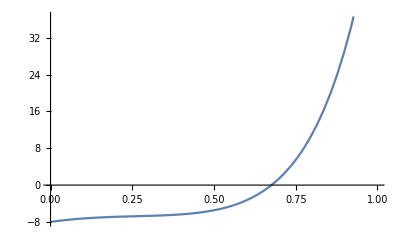

```mathematica
Plot[simple[a,5],{a,0,1}]
```

```mathematica
e = E
```

ⅇ

```mathematica
complexSum[L_,a_,b_] = Abs[Sum[e^(n (a+b I)), {n,0,L-1}]]
complexDiff[L_,a_,b_] = complexSum[L,a,b] - complexSum[L,-a,-b]
```

Abs[(-1+ⅇ^(a L+ⅈ b L))/(-1+ⅇ^(a+ⅈ b))]

-Abs[(-1+ⅇ^(-a L-ⅈ b L))/(-1+ⅇ^(-a-ⅈ b))]+Abs[(-1+ⅇ^(a+b i+a L+b i L))/(-1+ⅇ^(a+b i))]

```mathematica
ListAnimate[Table[Plot[complexDiff[5,a,b],{a,0,1}],{b,-10,10}]]
N[complexDiff[5,.0001,-10]]
```

-0.137994+Abs[(-1.+2.71828^(0.0006-60. i))/(-1.+2.71828^(0.0001-10. i))]

ⅇ

1+ⅇ^z+ⅇ^(2 z)+ⅇ^(3 z)+ⅇ^(4 z)+ⅇ^(5 z)+ⅇ^(6 z)

ⅇ^(2 z)+ⅇ^(3 z)+ⅇ^(4 z)

-Abs[ⅇ^(2 z)+ⅇ^(3 z)+ⅇ^(4 z)]+Abs[1+ⅇ^z+ⅇ^(2 z)+ⅇ^(3 z)+ⅇ^(4 z)+ⅇ^(5 z)+ⅇ^(6 z)]

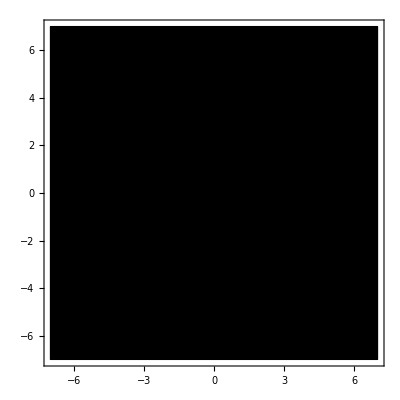

```mathematica
e = E
f[z_] = Sum[e^(n z), {n,0,6}]
g[z_] = e^(2 z) + e^(3 z) + e^(4z)
dif[z_] = Abs[f[z]] - Abs[g[z]]
ComplexPlot[dif[z],{z,-7-7I,7 +7 I},PlotLegends->Automatic]
```

```mathematica
e  = E
f[z_] = e^(3z) + e^(7z)
g[z_] = Abs[f[z]]^2 - (E^(2*3*Re[z])+E^(2*7*Re[z])+E^(10*Re[z])(2*Cos[4 Im[z]]))
```

ⅇ

ⅇ^(3 z)+ⅇ^(7 z)

-ⅇ^(6 Re[z])-ⅇ^(14 Re[z])+Abs[ⅇ^(3 z)+ⅇ^(7 z)]^2-2 ⅇ^(10 Re[z]) Cos[4 Im[z]]

```mathematica
ComplexPlot[g[z],{z,-7-7I,7 +7 I},PlotLegends->Automatic]
```

-Graphics-